```mathematica
(*No feedback parameters for Fig 1C, Fig 2A*)
p0=0.25;q0=0.2;p1=0.3;q1=0.01;v0=0.5;v1=1;d2=0.05;d0=0.1;d2=1;d1=0.5;
(*Equations for No Feedback*)
equA = (x0'[t]==(p0-q0)*v0*x0[t]-d0*x0[t]);
equB = (x1'[t]==(1-p0+q0)*v0*x0[t]+(p1-q1)*v1*x1[t]-d1*x1[t]);
equC = (x2'[t]==(1-p1+q1)*v1*x1[t]-d2*x2[t]);
(*No feedback figure results*)
initNumCells = 1.5*10^5;
noFeedbackResults = NDSolveValue[{equA,equB,equC,x0[0]==initNumCells,x1[0]==initNumCells,x2[0]==initNumCells},{x0,x1,x2},{t,0,20}];
noFeedbackNumCells[t_]:=noFeedbackResults[[1]][t]+noFeedbackResults[[2]][t]+noFeedbackResults[[3]][t];
```

```mathematica
(*Equations for Type I feedback*)
```

```mathematica
p0=0.5;q0=0.2;p1=0.5;q1=0.1;v0=0.5;v1=1;d2=0.05;d0=0.1;d1=0.5;d2=1;beta0=2*10^-11;beta1=3*10^-12; tau=2;
equ0=(x0'[t]==(p0-q0)(v0/(1+beta0*(x2[t-tau])^2))*x0[t]-d0*x0[t]);
equ1 = (x1'[t]==(1-p0+q0)*(v0/(1+beta0*(x2[t-tau])^2))*x0[t]+(p1-q1)(v1/(1+beta1*(x2[t-tau])^2))*x1[t]-d1*x1[t]);
equ2 = (x2'[t]==(1-p1+q1)(v1/(1+beta1*(x2[t-tau])^2))*x1[t]-d2*x2[t]);
typeIfeedbackResults = NDSolveValue[{equ0,equ1,equ2,x0[0]==initNumCells,x1[0]==initNumCells,x2[0]==initNumCells},{x0,x1,x2},{t,0,20}]
typeIfeedbackNumCells[t_]:=typeIfeedbackResults[[1]][t]+typeIfeedbackResults[[2]][t]+typeIfeedbackResults[[3]][t];
```

NDSolveValue::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>]}

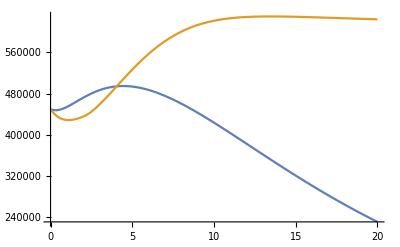

```mathematica
Plot[{noFeedbackNumCells[t],typeIfeedbackNumCells[t]},{t,0,20}]
```

```mathematica
(*Equations for Type II feedback*)
```

```mathematica
equ3 = (x0'[t]==(p0/(1+gamma10*(x2(t-tau))^2) - q0/(1+gamma20*(x2*(t-tau))^2))*v0*x0[t]-d0*x0[t]);
equ4 = (x1'[t]==(p0/(1+gamma10*(x2(t-tau))^2) - q0/(1+gamma20*(x2*(t-tau))^2))*v0*x0[t] + (p0/(1+gamma11*(x2(t-tau))^2) - q0/(1+gamma21*(x2*(t-tau))^2))*v1*x1[t]-d1*x1[t]);
equ5 = (x2'[t]==(1-p1/(1+gamma11*(x2(t-tau))^2) + q1/(1+gamma21*(x2*(t-tau))^2))*v1*x1[t]-d2*x2[t]);
```

```mathematica
(*Equation for Type I and Type II together*)
```

```mathematica
equ6 = (x0'[t]==(p0/(1+gamma10*(x2(t-tau))^2) - q0/(1+gamma20*(x2*(t-tau))^2))*(v0/(1+beta0*(x2(t-tau))^2))*x0[t]-d0*x0[t]);
equ7 = (x1'[t]==(1-p0/(1+gamma10*(x2(t-tau))^2) + q0/(1+gamma20*(x2*(t-tau))^2))*(v0/(1+beta0*(x2(t-tau))^2))*x0[t]+(p1/(1+gamma11*(x2(t-tau))^2) + q1/(1+gamma21*(x2*(t-tau))^2))*(v1/(1+beta1*(x2(t-tau))^2))*x1[t]-d1*x1[t]);
equ8 = (x2'[t]==(1-p1/(1+gamma11*(x2(t-tau))^2) + q1/(1+gamma21*(x2*(t-tau))^2))*(v1/(1+beta1*(x2(t-tau))^2))*x1[t]-d2*x2[t]);
```

{InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>]}

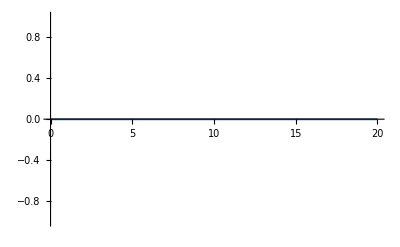

```mathematica
Plot[results[[1]][t],{t,0,20}]
```

```mathematica
equX1 = (y1'[t]==2*y1[t]+3y2[t])
equX2 = (y2'[t]==100*y1[t]-300y2[t])
```

y1'[t]==2 y1[t]+3 y2[t]

y2'[t]==100 y1[t]-300 y2[t]

```mathematica
res2 = NDSolveValue[{equX1,equX2,y1[0]==4,y2[0]==5},{y1,y2},{t,0,20}]
```

{InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>]}

```mathematica
Plot[res2[[1]][t],{t,0,20}]
```

-Graphics-